```mathematica
Needs["VectorFieldPlots`"];
SetDirectory[NotebookDirectory[]];
p=ReadList["H1.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
L=24;
Dimensions[p]
p=ArrayReshape[p,{300,L,L,3}];
chi=ConstantArray[0,{20,15}];
mag=ConstantArray[0,{20,15}];
```

{518400,1}

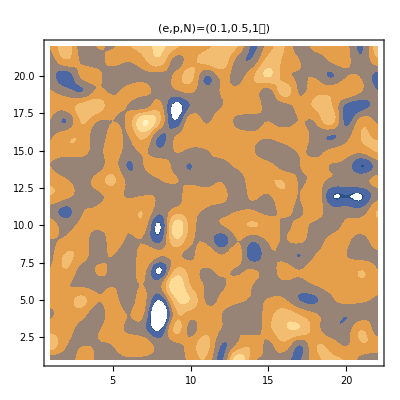
```mathematica
-Graphics-

For[n=1,n≤300,n++,
p2=p[[n,All,All,All]];
edge=1;
chirality=Table[p2[[i,j]].(
     Cross[p2[[i+1,j]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i,j+1]],p2[[i,j-1]]]
+Cross[p2[[i-1,j]],p2[[i-1,j-1]]]
+Cross[p2[[i,j-1]],p2[[i+1,j-1]]]
+Cross[p2[[i+1,j+1]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i-1,j-1]],p2[[i,j-1]]]
+Cross[p2[[i+1,j-1]],p2[[i+1,j]]]),{i,1+edge,L-edge},{j,1+edge,L-edge}];
chi[[Floor[n/15]+1,Mod[n-1,15]+1]]=Total[Total[chirality]]/(L*L);
mag[[Floor[n/15]+1,Mod[n-1,15]+1]]=Total[Total[p2[[All,All,3]]]]/(L*L)
]
MatrixPlot[chi]
MatrixPlot[mag]
```

-Graphics-

Set::partw: Part 21 of {{-0.00255781675446918, -0.1390987733612038, -0.1911763081274328, -0.30768497914288625, -0.38911929701015539, -0.4831946210559617, -« 58 », -« 59 », -« 59 », -« 59 », -0.97364075652856623, -1.0510239432481751, -1.1753505621943164, -1.197765361377611, 0}, {« 1 »}, « 17 », {« 1 »}} does not exist.

Set::partw: Part 21 of {{0.001152431494221492, 0.021664167404155919, 0.040531538814048103, 0.058478853821267523, 0.088197126342642818, 0.102544004056481612, « 59 », « 58 », « 59 », 0.20367081245322605, 0.228110727388804375, 0.245633071834057819, 0.261211916534583672, 0.294706201088629082, 0}, « 18 », {« 1 »}} does not exist.

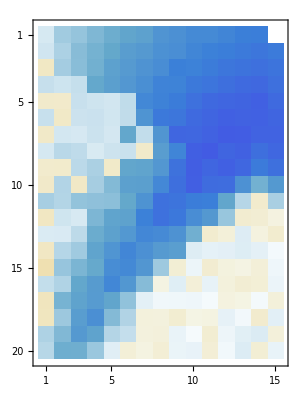

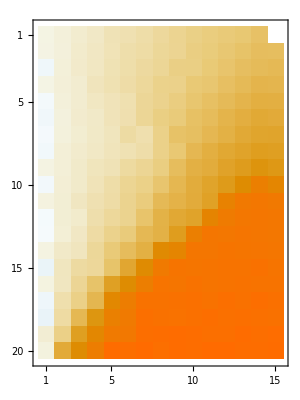

```mathematica
p2=p[[2,All,All,All]];
edge=1;
chirality=Table[p2[[i,j]].(
     Cross[p2[[i+1,j]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i,j+1]],p2[[i,j-1]]]
+Cross[p2[[i-1,j]],p2[[i-1,j-1]]]
+Cross[p2[[i,j-1]],p2[[i+1,j-1]]]
+Cross[p2[[i+1,j+1]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i-1,j-1]],p2[[i,j-1]]]
+Cross[p2[[i+1,j-1]],p2[[i+1,j]]]),{i,1+edge,L-edge},{j,1+edge,L-edge}];
ListContourPlot[chirality,PlotLabel->Style["(e,p,N)=(0.1,0.5,1만)",FontSize->20],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]
```

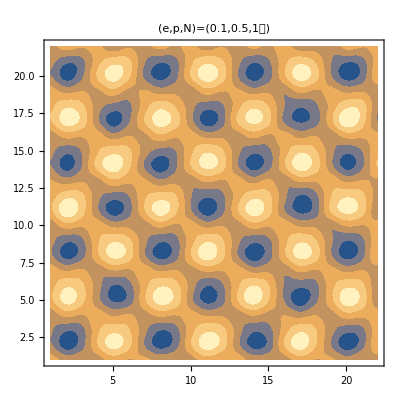
```mathematica
-Graphics-
ListPlot[chi[[1,All]]]
```

-Graphics-

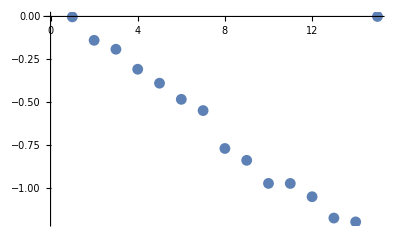

```mathematica
ListContourPlot[p2[[All,All,1]],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]ListContourPlot[p2[[All,All,2]],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]ListContourPlot[p2[[All,All,3]],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]

coord =Flatten[Table[{x,y},{x,1,L,1},{y,1,L,1}],1];
CONFnewlist=Table[{{coord[[i]][[1]],coord[[i]][[2]],0},Flatten[p2,1][[i]]},{i,L*L}];
ListVectorFieldPlot3D[CONFnewlist,ScaleFactor->1,VectorHeads->True]
```

-Graphics- -Graphics- -Graphics-

-Graphics3D-